# Machine Learning Template for Classifying

-Graphics-

Data source: https://www.kaggle.com/mansoordaku/ckdisease

Import from a Excel file

```mathematica
(*import file*)
(*SetDirectory["C:\\Users\\yap\\Downloads\\New folder (2)\\practice"]*)
(*importfile = Import["kidney_disease.xlsx",{"Data",1}],[[3;;]];*)
SetDirectory[NotebookDirectory[]];
myImport=Import["kidney_disease.xlsx",{"Data",1}] [[3;;]];
myHeader=Import["kidney_disease.xlsx",{"Data",1}] [[1;;2]];
```

Use correlation matrix to determine the important input parameters

Quick Data Transformation

```mathematica
(*transform dataset into aa list *)
myData=Thread[myImport[[1;;,1;;-2]]->myImport[[1;;,-1]]];
```

```mathematica
%104
```

{{48.,80.,1.02,1.,0.,,normal,0.,0.,121.,36.,1.2,,,15.4,44.,7800.,5.2,1.,1.,0.,good,0.,0.,ckd},{7.,50.,1.02,4.,0.,,normal,0.,0.,,18.,0.8,,,11.3,38.,6000.,,0.,0.,0.,good,0.,0.,ckd},{62.,80.,1.01,2.,3.,normal,normal,0.,0.,423.,53.,1.8,,,9.6,31.,7500.,,0.,1.,0.,poor,0.,1.,ckd},{48.,70.,1.005,4.,0.,normal,abnormal,1.,0.,117.,56.,3.8,111.,2.5,11.2,32.,6700.,3.9,1.,0.,0.,poor,1.,1.,ckd},{51.,80.,1.01,2.,0.,normal,normal,0.,0.,106.,26.,1.4,,,11.6,35.,7300.,4.6,0.,0.,0.,good,0.,0.,ckd},{60.,90.,1.015,3.,0.,,,0.,0.,74.,25.,1.1,142.,3.2,12.2,39.,7800.,4.4,1.,1.,0.,good,1.,0.,ckd},{68.,70.,1.01,0.,0.,,normal,0.,0.,100.,54.,24.,104.,4.,12.4,36.,,,0.,0.,0.,good,0.,0.,ckd},{24.,,1.015,2.,4.,normal,abnormal,0.,0.,410.,31.,1.1,,,12.4,44.,6900.,5.,0.,1.,0.,good,1.,0.,ckd},{52.,100.,1.015,3.,0.,normal,abnormal,1.,0.,138.,60.,1.9,,,10.8,33.,9600.,4.,1.,1.,0.,good,0.,1.,ckd},{53.,90.,1.02,2.,0.,abnormal,abnormal,1.,0.,70.,107.,7.2,114.,3.7,9.5,29.,12100.,3.7,1.,1.,0.,poor,0.,1.,ckd},{50.,60.,1.01,2.,4.,,abnormal,1.,0.,490.,55.,4.,,,9.4,28.,,,1.,1.,0.,good,0.,1.,ckd},{63.,70.,1.01,3.,0.,abnormal,abnormal,1.,0.,380.,60.,2.7,131.,4.2,10.8,32.,4500.,3.8,1.,1.,0.,poor,1.,0.,ckd},{68.,70.,1.015,3.,1.,,normal,1.,0.,208.,72.,2.1,138.,5.8,9.7,28.,12200.,3.4,1.,1.,1.,poor,1.,0.,ckd},{68.,70.,,,,,,0.,0.,98.,86.,4.6,135.,3.4,9.8,,,,1.,1.,1.,poor,1.,0.,ckd},{68.,80.,1.01,3.,2.,normal,abnormal,1.,1.,157.,90.,4.1,130.,6.4,5.6,16.,11000.,2.6,1.,1.,1.,poor,1.,0.,ckd},{40.,80.,1.015,3.,0.,,normal,0.,0.,76.,162.,9.6,141.,4.9,7.6,24.,3800.,2.8,1.,0.,0.,good,0.,1.,ckd},{47.,70.,1.015,2.,0.,,normal,0.,0.,99.,46.,2.2,138.,4.1,12.6,,,,0.,0.,0.,good,0.,0.,ckd},{47.,80.,,,,,,0.,0.,114.,87.,5.2,139.,3.7,12.1,,,,1.,0.,0.,poor,0.,0.,ckd},{60.,100.,1.025,0.,3.,,normal,0.,0.,263.,27.,1.3,135.,4.3,12.7,37.,11400.,4.3,1.,1.,1.,good,0.,0.,ckd},{62.,60.,1.015,1.,0.,,abnormal,1.,0.,100.,31.,1.6,,,10.3,30.,5300.,3.7,1.,0.,1.,good,0.,0.,ckd},{61.,80.,1.015,2.,0.,abnormal,abnormal,0.,0.,173.,148.,3.9,135.,5.2,7.7,24.,9200.,3.2,1.,1.,1.,poor,1.,1.,ckd},{60.,90.,,,,,,0.,0.,,180.,76.,4.5,,10.9,32.,6200.,3.6,1.,1.,1.,good,0.,0.,ckd},{48.,80.,1.025,4.,0.,normal,abnormal,0.,0.,95.,163.,7.7,136.,3.8,9.8,32.,6900.,3.4,1.,0.,0.,good,0.,1.,ckd},{21.,70.,1.01,0.,0.,,normal,0.,0.,,,,,,,,,,0.,0.,0.,poor,0.,1.,ckd},{42.,100.,1.015,4.,0.,normal,abnormal,0.,1.,,50.,1.4,129.,4.,11.1,39.,8300.,4.6,1.,0.,0.,poor,0.,0.,ckd},{61.,60.,1.025,0.,0.,,normal,0.,0.,108.,75.,1.9,141.,5.2,9.9,29.,8400.,3.7,1.,1.,0.,good,0.,1.,ckd},{75.,80.,1.015,0.,0.,,normal,0.,0.,156.,45.,2.4,140.,3.4,11.6,35.,10300.,4.,1.,1.,0.,poor,0.,0.,ckd},{69.,70.,1.01,3.,4.,normal,abnormal,0.,0.,264.,87.,2.7,130.,4.,12.5,37.,9600.,4.1,1.,1.,1.,good,1.,0.,ckd},{75.,70.,,1.,3.,,,0.,0.,123.,31.,1.4,,,,,,,0.,1.,0.,good,0.,0.,ckd},{68.,70.,1.005,1.,0.,abnormal,abnormal,1.,0.,,28.,1.4,,,12.9,38.,,,0.,0.,1.,good,0.,0.,ckd},{,70.,,,,,,0.,0.,93.,155.,7.3,132.,4.9,,,,,1.,1.,0.,good,0.,0.,ckd},{73.,90.,1.015,3.,0.,,abnormal,1.,0.,107.,33.,1.5,141.,4.6,10.1,30.,7800.,4.,0.,0.,0.,poor,0.,0.,ckd},{61.,90.,1.01,1.,1.,,normal,0.,0.,159.,39.,1.5,133.,4.9,11.3,34.,9600.,4.,1.,1.,0.,poor,0.,0.,ckd},{60.,100.,1.02,2.,0.,abnormal,abnormal,0.,0.,140.,55.,2.5,,,10.1,29.,,,1.,0.,0.,poor,0.,0.,ckd},{70.,70.,1.01,1.,0.,normal,,1.,1.,171.,153.,5.2,,,,,,,0.,1.,0.,poor,0.,0.,ckd},{65.,90.,1.02,2.,1.,abnormal,normal,0.,0.,270.,39.,2.,,,12.,36.,9800.,4.9,1.,1.,0.,poor,0.,1.,ckd},{76.,70.,1.015,1.,0.,normal,normal,0.,0.,92.,29.,1.8,133.,3.9,10.3,32.,,,1.,0.,0.,good,0.,0.,ckd},{72.,80.,,,,,,0.,0.,137.,65.,3.4,141.,4.7,9.7,28.,6900.,2.5,1.,1.,0.,poor,0.,1.,ckd	},{69.,80.,1.02,3.,0.,abnormal,normal,0.,0.,,103.,4.1,132.,5.9,12.5,,,,1.,0.,0.,good,0.,0.,ckd},{82.,80.,1.01,2.,2.,normal,,0.,0.,140.,70.,3.4,136.,4.2,13.,40.,9800.,4.2,1.,1.,0.,good,0.,0.,ckd},{46.,90.,1.01,2.,0.,normal,abnormal,0.,0.,99.,80.,2.1,,,11.1,32.,9100.,4.1,1.,0.,	0,good,0.,0.,ckd},{45.,70.,1.01,0.,0.,,normal,0.,0.,,20.,0.7,,,,,,,0.,0.,0.,good,1.,0.,ckd},{47.,100.,1.01,0.,0.,,normal,0.,0.,204.,29.,1.,139.,4.2,9.7,33.,9200.,4.5,1.,0.,0.,good,0.,1.,ckd},{35.,80.,1.01,1.,0.,abnormal,,0.,0.,79.,202.,10.8,134.,3.4,7.9,24.,7900.,3.1,0.,1.,0.,good,0.,0.,ckd},{54.,80.,1.01,3.,0.,abnormal,abnormal,0.,0.,207.,77.,6.3,134.,4.8,9.7,28.,,,1.,1.,0.,poor,1.,0.,ckd},{54.,80.,1.02,3.,0.,,abnormal,0.,0.,208.,89.,5.9,130.,4.9,9.3,,,,1.,1.,0.,poor,1.,0.,ckd},{48.,70.,1.015,0.,0.,,normal,0.,0.,124.,24.,1.2,142.,4.2,12.4,37.,6400.,4.7,0.,1.,0.,good,0.,0.,ckd},{11.,80.,1.01,3.,0.,,normal,0.,0.,,17.,0.8,,,15.,45.,8600.,,0.,0.,0.,good,0.,0.,ckd},{73.,70.,1.005,0.,0.,normal,normal,0.,0.,70.,32.,0.9,125.,4.,10.,29.,18900.,3.5,1.,1.,0.,good,1.,0.,ckd},{60.,70.,1.01,2.,0.,normal,abnormal,1.,0.,144.,72.,3.,,,9.7,29.,21600.,3.5,1.,1.,0.,poor,0.,1.,ckd},{53.,60.,,,,,,0.,0.,91.,114.,3.25,142.,4.3,8.6,28.,11000.,3.8,1.,1.,0.,poor,1.,1.,ckd},{54.,100.,1.015,3.,0.,,normal,1.,0.,162.,66.,1.6,136.,4.4,10.3,33.,,,1.,1.,0.,poor,1.,0.,ckd},{53.,90.,1.015,0.,0.,,normal,0.,0.,,38.,2.2,,,10.9,34.,4300.,3.7,0.,0.,0.,poor,0.,1.,ckd},{62.,80.,1.015,0.,5.,,,0.,0.,246.,24.,1.,,,13.6,40.,8500.,4.7,1.,1.,0.,good,0.,0.,ckd},{63.,80.,1.01,2.,2.,normal,,0.,0.,,,3.4,136.,4.2,13.,40.,9800.,4.2,1.,0.,1.,good,0.,0.,ckd},{35.,80.,1.005,3.,0.,abnormal,normal,0.,0.,,,,,,9.5,28.,,,0.,0.,0.,good,1.,0.,ckd},{76.,70.,1.015,3.,4.,normal,abnormal,1.,0.,,164.,9.7,131.,4.4,10.2,30.,11300.,3.4,1.,1.,1.,poor,1.,0.,ckd},{76.,90.,,,,,normal,0.,0.,93.,155.,7.3,132.,4.9,,,,,1.,1.,1.,poor,0.,0.,ckd},{73.,80.,1.02,2.,0.,abnormal,abnormal,0.,0.,253.,142.,4.6,138.,5.8,10.5,33.,7200.,4.3,1.,1.,1.,good,0.,0.,ckd},{59.,100.,,,,,,0.,0.,,96.,6.4,,,6.6,,,,1.,1.,0.,good,0.,1.,ckd},{67.,90.,1.02,1.,0.,,abnormal,1.,0.,141.,66.,3.2,138.,6.6,,,,,1.,0.,0.,good,0.,0.,ckd},{67.,80.,1.01,1.,3.,normal,abnormal,0.,0.,182.,391.,32.,163.,39.,,,,,0.,0.,0.,good,1.,0.,ckd},{15.,60.,1.02,3.,0.,,normal,0.,0.,86.,15.,0.6,138.,4.,11.,33.,7700.,3.8,1.,1.,0.,good,0.,0.,ckd},{46.,70.,1.015,1.,0.,abnormal,normal,0.,0.,150.,111.,6.1,131.,3.7,7.5,27.,,,0.,0.,0.,good,0.,1.,ckd},{55.,80.,1.01,0.,0.,,normal,0.,0.,146.,,,,,9.8,,,,0.,0.,	0,good,0.,0.,ckd},{44.,90.,1.01,1.,0.,,normal,0.,0.,,20.,1.1,,,15.,48.,,,0.,	0,0.,good,0.,0.,ckd},{67.,70.,1.02,2.,0.,abnormal,normal,0.,0.,150.,55.,1.6,131.,4.8,,	?,,,1.,1.,0.,good,1.,0.,ckd},{45.,80.,1.02,3.,0.,normal,abnormal,0.,0.,425.,,,,,,,,,0.,0.,0.,poor,0.,0.,ckd},{65.,70.,1.01,2.,0.,,normal,1.,0.,112.,73.,3.3,,,10.9,37.,,,0.,0.,0.,good,0.,0.,ckd},{26.,70.,1.015,0.,4.,,normal,0.,0.,250.,20.,1.1,,,15.6,52.,6900.,6.,0.,1.,0.,good,0.,0.,ckd},{61.,80.,1.015,0.,4.,,normal,0.,0.,360.,19.,0.7,137.,4.4,15.2,44.,8300.,5.2,1.,1.,0.,good,0.,0.,ckd},{46.,60.,1.01,1.,0.,normal,normal,0.,0.,163.,92.,3.3,141.,4.,9.8,28.,14600.,3.2,1.,1.,0.,good,0.,0.,ckd},{64.,90.,1.01,3.,3.,,abnormal,1.,0.,,35.,1.3,,,10.3,,,,1.,1.,0.,good,1.,0.,ckd},{,100.,1.015,2.,0.,abnormal,abnormal,0.,0.,129.,107.,6.7,132.,4.4,4.8,14.,6300.,,1.,0.,0.,good,1.,1.,ckd},{56.,90.,1.015,2.,0.,abnormal,abnormal,0.,0.,129.,107.,6.7,131.,4.8,9.1,29.,6400.,3.4,1.,0.,0.,good,0.,0.,ckd},{5.,,1.015,1.,0.,,normal,0.,0.,,16.,0.7,138.,3.2,8.1,,,,0.,0.,0.,good,0.,1.,ckd},{48.,80.,1.005,4.,0.,abnormal,abnormal,0.,1.,133.,139.,8.5,132.,5.5,10.3,36.,	6200,4.,0.,1.,0.,good,1.,0.,ckd},{67.,70.,1.01,1.,0.,,normal,0.,0.,102.,48.,3.2,137.,5.,11.9,34.,7100.,3.7,1.,1.,0.,good,1.,0.,ckd},{70.,80.,,,,,,0.,0.,158.,85.,3.2,141.,3.5,10.1,30.,,,1.,0.,0.,good,1.,0.,ckd},{56.,80.,1.01,1.,0.,,normal,0.,0.,165.,55.,1.8,,,13.5,40.,11800.,5.,1.,1.,0.,poor,1.,0.,ckd},{74.,80.,1.01,0.,0.,,normal,0.,0.,132.,98.,2.8,133.,5.,10.8,31.,9400.,3.8,1.,1.,0.,good,0.,0.,ckd},{45.,90.,,,,,,0.,0.,360.,45.,2.4,128.,4.4,8.3,29.,5500.,3.7,1.,1.,0.,good,0.,0.,ckd},{38.,70.,,,,,,0.,0.,104.,77.,1.9,140.,3.9,,,,,1.,0.,0.,poor,1.,0.,ckd},{48.,70.,1.015,1.,0.,normal,normal,0.,0.,127.,19.,1.,134.,3.6,,,,,1.,1.,0.,good,0.,0.,ckd},{59.,70.,1.01,3.,0.,normal,abnormal,0.,0.,76.,186.,15.,135.,7.6,7.1,22.,3800.,2.1,1.,0.,0.,poor,1.,1.,ckd},{70.,70.,1.015,2.,,,,0.,0.,,46.,1.5,,,9.9,,,,0.,1.,0.,poor,1.,0.,ckd},{56.,80.,,,,,,0.,0.,415.,37.,1.9,,,,,,,0.,1.,0.,good,0.,0.,ckd},{70.,100.,1.005,1.,0.,normal,abnormal,1.,0.,169.,47.,2.9,,,11.1,32.,5800.,5.,1.,1.,0.,poor,0.,0.,ckd},{58.,110.,1.01,4.,0.,,normal,0.,0.,251.,52.,2.2,,,,,13200.,4.7,1.,	1,0.,good,0.,0.,ckd},{50.,70.,1.02,0.,0.,,normal,0.,0.,109.,32.,1.4,139.,4.7,,,,,0.,0.,0.,poor,0.,0.,ckd},{63.,100.,1.01,2.,2.,normal,normal,0.,1.,280.,35.,3.2,143.,3.5,13.,40.,9800.,4.2,1.,0.,1.,good,0.,0.,ckd},{56.,70.,1.015,4.,1.,abnormal,normal,0.,0.,210.,26.,1.7,136.,3.8,16.1,52.,12500.,5.6,0.,0.,0.,good,0.,0.,ckd},{71.,70.,1.01,3.,0.,normal,abnormal,1.,1.,219.,82.,3.6,133.,4.4,10.4,33.,5600.,3.6,1.,1.,1.,good,0.,0.,ckd},{73.,100.,1.01,3.,2.,abnormal,abnormal,1.,0.,295.,90.,5.6,140.,2.9,9.2,30.,7000.,3.2,1.,1.,1.,poor,0.,0.,ckd},{65.,70.,1.01,0.,0.,,normal,0.,0.,93.,66.,1.6,137.,4.5,11.6,36.,11900.,3.9,0.,1.,0.,good,0.,0.,ckd},{62.,90.,1.015,1.,0.,,normal,0.,0.,94.,25.,1.1,131.,3.7,,,,,1.,0.,0.,good,1.,1.,ckd},{60.,80.,1.01,1.,1.,,normal,0.,0.,172.,32.,2.7,,,11.2,36.,,,0.,1.,1.,poor,0.,0.,ckd},{65.,60.,1.015,1.,0.,,normal,0.,0.,91.,51.,2.2,132.,3.8,10.,32.,9100.,4.,1.,1.,0.,poor,1.,0.,ckd},{50.,140.,,,,,,0.,0.,101.,106.,6.5,135.,4.3,6.2,18.,5800.,2.3,1.,1.,0.,poor,0.,1.,ckd},{56.,180.,,0.,4.,,abnormal,0.,0.,298.,24.,1.2,139.,3.9,11.2,32.,10400.,4.2,1.,1.,0.,poor,1.,0.,ckd},{34.,70.,1.015,4.,0.,abnormal,abnormal,0.,0.,153.,22.,0.9,133.,3.8,,,,,0.,0.,0.,good,1.,0.,ckd},{71.,90.,1.015,2.,0.,,abnormal,1.,1.,88.,80.,4.4,139.,5.7,11.3,33.,10700.,3.9,0.,0.,0.,good,0.,0.,ckd},{17.,60.,1.01,0.,0.,,normal,0.,0.,92.,32.,2.1,141.,4.2,13.9,52.,7000.,,0.,0.,0.,good,0.,0.,ckd},{76.,70.,1.015,2.,0.,normal,abnormal,1.,0.,226.,217.,10.2,,,10.2,36.,12700.,4.2,1.,0.,0.,poor,1.,1.,ckd},{55.,90.,,,,,,0.,0.,143.,88.,2.,,,,,,,1.,1.,0.,poor,1.,0.,ckd},{65.,80.,1.015,0.,0.,,normal,0.,0.,115.,32.,11.5,139.,4.,14.1,42.,6800.,5.2,0.,0.,0.,good,0.,0.,ckd},{50.,90.,,,,,,0.,0.,89.,118.,6.1,127.,4.4,6.,17.,6500.,,1.,1.,0.,good,1.,1.,ckd},{55.,100.,1.015,1.,4.,normal,,0.,0.,297.,53.,2.8,139.,4.5,11.2,34.,13600.,4.4,1.,1.,0.,good,0.,0.,ckd},{45.,80.,1.015,0.,0.,,abnormal,0.,0.,107.,15.,1.,141.,4.2,11.8,37.,10200.,4.2,0.,0.,0.,good,0.,0.,ckd},{54.,70.,,,,,,0.,0.,233.,50.1,1.9,,,11.7,,,,0.,1.,0.,good,0.,0.,ckd},{63.,90.,1.015,0.,0.,,normal,0.,0.,123.,19.,2.,142.,3.8,11.7,34.,11400.,4.7,0.,0.,0.,good,0.,0.,ckd},{65.,80.,1.01,3.,3.,,normal,0.,0.,294.,71.,4.4,128.,5.4,10.,32.,9000.,3.9,1.,1.,1.,good,0.,0.,ckd},{,60.,1.015,3.,0.,abnormal,abnormal,0.,0.,,34.,1.2,,,10.8,33.,,,0.,0.,0.,good,0.,0.,ckd},{61.,90.,1.015,0.,2.,,normal,0.,0.,,,,,,,,9800.,,0.,1.,0.,poor,0.,1.,ckd},{12.,60.,1.015,3.,0.,abnormal,abnormal,1.,0.,,51.,1.8,,,12.1,,10300.,,0.,0.,0.,good,0.,0.,ckd},{47.,80.,1.01,0.,0.,,abnormal,0.,0.,,28.,0.9,,,12.4,44.,5600.,4.3,0.,0.,0.,good,0.,1.,ckd},{,70.,1.015,4.,0.,abnormal,normal,0.,0.,104.,16.,0.5,,,,,,,0.,0.,0.,good,1.,0.,ckd},{,70.,1.02,0.,0.,,,0.,0.,219.,36.,1.3,139.,3.7,12.5,37.,9800.,4.4,0.,0.,0.,good,0.,0.,ckd},{55.,70.,1.01,3.,0.,,normal,0.,0.,99.,25.,1.2,,,11.4,,,,0.,0.,0.,poor,1.,0.,ckd},{60.,70.,1.01,0.,0.,,normal,0.,0.,140.,27.,1.2,,,,,,,0.,0.,0.,good,0.,0.,ckd},{72.,90.,1.025,1.,3.,,normal,0.,0.,323.,40.,2.2,137.,5.3,12.6,,,,0.,1.,1.,poor,0.,0.,ckd},{54.,60.,,3.,,,,0.,0.,125.,21.,1.3,137.,3.4,15.,46.,,,1.,1.,0.,good,1.,0.,ckd},{34.,70.,,,,,,0.,0.,,219.,12.2,130.,3.8,6.,,,,1.,0.,0.,good,0.,1.,ckd},{43.,80.,1.015,2.,3.,,abnormal,1.,1.,,30.,1.1,,,14.,42.,14900.,,0.,0.,0.,good,0.,0.,ckd},{65.,100.,1.015,0.,0.,,normal,0.,0.,90.,98.,2.5,,,9.1,28.,5500.,3.6,1.,0.,0.,good,0.,0.,ckd},{72.,90.,,,,,,0.,0.,308.,36.,2.5,131.,4.3,,,,,1.,1.,0.,poor,0.,0.,ckd},{70.,90.,1.015,0.,0.,,normal,0.,0.,144.,125.,4.,136.,4.6,12.,37.,8200.,4.5,1.,1.,0.,poor,1.,0.,ckd},{71.,60.,1.015,4.,0.,normal,normal,0.,0.,118.,125.,5.3,136.,4.9,11.4,35.,15200.,4.3,1.,1.,0.,poor,1.,0.,ckd},{52.,90.,1.015,4.,3.,normal,abnormal,0.,0.,224.,166.,5.6,133.,47.,8.1,23.,5000.,2.9,1.,1.,0.,good,0.,1.,ckd},{75.,70.,1.025,1.,0.,,normal,0.,0.,158.,49.,1.4,135.,4.7,11.1,,,,1.,0.,0.,poor,1.,0.,ckd},{50.,90.,1.01,2.,0.,normal,abnormal,1.,1.,128.,208.,9.2,134.,4.8,8.2,22.,16300.,2.7,0.,0.,0.,poor,1.,1.,ckd},{5.,50.,1.01,0.,0.,,normal,0.,0.,,25.,0.6,,,11.8,36.,12400.,,0.,0.,0.,good,0.,0.,ckd},{50.,,,,,normal,,0.,0.,219.,176.,13.8,136.,4.5,8.6,24.,13200.,2.7,1.,0.,0.,good,1.,1.,ckd},{70.,100.,1.015,4.,0.,normal,normal,0.,0.,118.,125.,5.3,136.,4.9,12.,37.,	8400,8.,1.,0.,0.,good,0.,0.,ckd},{47.,100.,1.01,,,normal,,0.,0.,122.,,16.9,138.,5.2,10.8,33.,10200.,3.8,0.,1.,0.,good,0.,0.,ckd},{48.,80.,1.015,0.,2.,,normal,0.,0.,214.,24.,1.3,140.,4.,13.2,39.,,,0.,1.,0.,poor,0.,0.,ckd},{46.,90.,1.02,,,,normal,0.,0.,213.,68.,2.8,146.,6.3,9.3,,,,1.,1.,0.,good,0.,0.,ckd},{45.,60.,1.01,2.,0.,normal,abnormal,1.,0.,268.,86.,4.,134.,5.1,10.,29.,9200.,,1.,1.,0.,good,0.,0.,ckd},{73.,,1.01,1.,0.,,,0.,0.,95.,51.,1.6,142.,3.5,,,,,0.,	0,0.,good,0.,0.,ckd},{41.,70.,1.015,2.,0.,,abnormal,0.,1.,,68.,2.8,132.,4.1,11.1,33.,,,1.,0.,0.,good,1.,1.,ckd},{69.,70.,1.01,0.,4.,,normal,0.,0.,256.,40.,1.2,142.,5.6,,,,,0.,0.,0.,good,0.,0.,ckd},{67.,70.,1.01,1.,0.,normal,normal,0.,0.,,106.,6.,137.,4.9,6.1,19.,6500.,,1.,0.,0.,good,0.,1.,ckd},{72.,90.,,,,,,0.,0.,84.,145.,7.1,135.,5.3,,,,,0.,1.,0.,good,0.,0.,ckd},{41.,80.,1.015,1.,4.,abnormal,normal,0.,0.,210.,165.,18.,135.,4.7,,,,,0.,1.,0.,good,0.,0.,ckd},{60.,90.,1.01,2.,0.,abnormal,normal,0.,0.,105.,53.,2.3,136.,5.2,11.1,33.,10500.,4.1,0.,0.,0.,good,0.,0.,ckd},{57.,90.,1.015,5.,0.,abnormal,abnormal,0.,1.,,322.,13.,126.,4.8,8.,24.,4200.,3.3,1.,1.,1.,poor,1.,1.,ckd},{53.,100.,1.01,1.,3.,abnormal,normal,0.,0.,213.,23.,1.,139.,4.,,,,,0.,1.,0.,good,0.,0.,ckd},{60.,60.,1.01,3.,1.,normal,abnormal,1.,0.,288.,36.,1.7,130.,3.,7.9,25.,15200.,3.,1.,0.,0.,poor,0.,1.,ckd},{69.,60.,,,,,,0.,0.,171.,26.,48.1,,,,,,,1.,0.,0.,poor,0.,0.,ckd},{65.,70.,1.02,1.,0.,abnormal,abnormal,0.,0.,139.,29.,1.,,,10.5,32.,,,1.,0.,0.,good,1.,0.,ckd},{8.,60.,1.025,3.,0.,normal,normal,0.,0.,78.,27.,0.9,,,12.3,41.,6700.,,0.,0.,0.,poor,1.,0.,ckd},{76.,90.,,,,,,0.,0.,172.,46.,1.7,141.,5.5,9.6,30.,,,1.,1.,0.,good,0.,1.,ckd},{39.,70.,1.01,0.,0.,,normal,0.,0.,121.,20.,0.8,133.,3.5,10.9,32.,,,0.,1.,0.,good,0.,0.,ckd},{55.,90.,1.01,2.,1.,abnormal,abnormal,0.,0.,273.,235.,14.2,132.,3.4,8.3,22.,14600.,2.9,1.,1.,0.,poor,1.,1.,ckd},{56.,90.,1.005,4.,3.,abnormal,abnormal,0.,0.,242.,132.,16.4,140.,4.2,8.4,26.,,3.,1.,1.,0.,poor,1.,1.,ckd},{50.,70.,1.02,3.,0.,abnormal,normal,1.,1.,123.,40.,1.8,,,11.1,36.,4700.,,0.,0.,0.,good,0.,0.,ckd},{66.,90.,1.015,2.,0.,,normal,0.,1.,153.,76.,3.3,,,,,,,0.,0.,0.,poor,0.,0.,ckd},{62.,70.,1.025,3.,0.,normal,abnormal,0.,0.,122.,42.,1.7,136.,4.7,12.6,39.,7900.,3.9,1.,1.,0.,good,0.,0.,ckd},{71.,60.,1.02,3.,2.,normal,normal,1.,0.,424.,48.,1.5,132.,4.,10.9,31.,,,1.,1.,1.,good,0.,0.,ckd},{59.,80.,1.01,1.,0.,abnormal,normal,0.,0.,303.,35.,1.3,122.,3.5,10.4,35.,10900.,4.3,0.,1.,0.,poor,0.,0.,ckd},{81.,60.,,,,,,0.,0.,148.,39.,2.1,147.,4.2,10.9,35.,9400.,2.4,1.,1.,1.,poor,1.,0.,ckd},{62.,,1.015,3.,0.,abnormal,,0.,0.,,,,,,14.3,42.,10200.,4.8,1.,1.,0.,good,0.,0.,ckd},{59.,70.,,,,,,0.,0.,204.,34.,1.5,124.,4.1,9.8,37.,6000.,,0.,1.,0.,good,0.,0.,ckd},{46.,80.,1.01,0.,0.,,normal,0.,0.,160.,40.,2.,140.,4.1,9.,27.,8100.,3.2,1.,0.,0.,poor,0.,1.,ckd},{14.,,1.015,0.,0.,,,0.,0.,192.,15.,0.8,137.,4.2,14.3,40.,9500.,5.4,0.,1.,0.,poor,1.,0.,ckd},{60.,80.,1.02,0.,2.,,,0.,0.,,,,,,,,,,0.,1.,0.,good,0.,0.,ckd},{27.,60.,,,,,,0.,0.,76.,44.,3.9,127.,4.3,,,,,0.,0.,0.,poor,1.,1.,ckd},{34.,70.,1.02,0.,0.,abnormal,normal,0.,0.,139.,19.,0.9,,,12.7,42.,2200.,,0.,0.,0.,poor,0.,0.,ckd},{65.,70.,1.015,4.,4.,,normal,1.,0.,307.,28.,1.5,,,11.,39.,6700.,,1.,1.,0.,good,0.,0.,ckd},{,70.,1.01,0.,2.,,normal,0.,0.,220.,68.,2.8,,,8.7,27.,,,1.,1.,0.,good,0.,1.,ckd},{66.,70.,1.015,2.,5.,,normal,0.,0.,447.,41.,1.7,131.,3.9,12.5,33.,9600.,4.4,1.,1.,0.,good,0.,0.,ckd},{83.,70.,1.02,3.,0.,normal,normal,0.,0.,102.,60.,2.6,115.,5.7,8.7,26.,12800.,3.1,1.,0.,0.,poor,0.,1.,ckd},{62.,80.,1.01,1.,2.,,,0.,0.,309.,113.,2.9,130.,2.5,10.6,34.,12800.,4.9,0.,0.,0.,good,0.,0.,ckd},{17.,70.,1.015,1.,0.,abnormal,normal,0.,0.,22.,1.5,7.3,145.,2.8,13.1,41.,11200.,,0.,0.,0.,good,0.,0.,ckd},{54.,70.,,,,,,0.,0.,111.,146.,7.5,141.,4.7,11.,35.,8600.,4.6,0.,0.,0.,good,0.,0.,ckd},{60.,50.,1.01,0.,0.,,normal,0.,0.,261.,58.,2.2,113.,3.,,,4200.,3.4,1.,0.,0.,good,0.,0.,ckd},{21.,90.,1.01,4.,0.,normal,abnormal,1.,1.,107.,40.,1.7,125.,3.5,8.3,23.,12400.,3.9,0.,0.,0.,good,0.,1.,ckd},{65.,80.,1.015,2.,1.,normal,normal,1.,0.,215.,133.,2.5,,,13.2,41.,,,0.,1.,0.,good,0.,0.,ckd},{42.,90.,1.02,2.,0.,abnormal,abnormal,1.,0.,93.,153.,2.7,139.,4.3,9.8,34.,9800.,,0.,0.,0.,poor,1.,1.,ckd},{72.,90.,1.01,2.,0.,,abnormal,1.,0.,124.,53.,2.3,,,11.9,39.,,,0.,0.,0.,good,0.,0.,ckd},{73.,90.,1.01,1.,4.,abnormal,abnormal,1.,0.,234.,56.,1.9,,,10.3,28.,,,0.,1.,0.,good,0.,0.,ckd},{45.,70.,1.025,2.,0.,normal,abnormal,1.,0.,117.,52.,2.2,136.,3.8,10.,30.,19100.,3.7,0.,0.,0.,good,0.,0.,ckd},{61.,80.,1.02,0.,0.,,normal,0.,0.,131.,23.,0.8,140.,4.1,11.3,35.,,,0.,0.,0.,good,0.,0.,ckd},{30.,70.,1.015,0.,0.,,normal,0.,0.,101.,106.,6.5,135.,4.3,,,,,0.,0.,0.,poor,0.,0.,ckd},{54.,60.,1.015,3.,2.,,abnormal,0.,0.,352.,137.,3.3,133.,4.5,11.3,31.,5800.,3.6,1.,1.,1.,poor,1.,0.,ckd},{4.,,1.02,1.,0.,,normal,0.,0.,99.,23.,0.6,138.,4.4,12.,34.,,,0.,0.,0.,good,0.,0.,ckd},{8.,50.,1.02,4.,0.,normal,normal,0.,0.,,46.,1.,135.,3.8,,,,,0.,0.,0.,good,1.,0.,ckd},{3.,,1.01,2.,0.,normal,normal,0.,0.,,22.,0.7,,,10.7,34.,12300.,,0.,0.,0.,good,0.,0.,ckd},{8.,,,,,,,0.,0.,80.,66.,2.5,142.,3.6,12.2,38.,,,0.,	0,0.,good,0.,0.,ckd},{64.,60.,1.01,4.,1.,abnormal,abnormal,0.,1.,239.,58.,4.3,137.,5.4,9.5,29.,7500.,3.4,1.,1.,0.,poor,1.,0.,ckd},{6.,60.,1.01,4.,0.,abnormal,abnormal,0.,1.,94.,67.,1.,135.,4.9,9.9,30.,16700.,4.8,0.,0.,0.,poor,0.,0.,ckd},{,70.,1.01,3.,0.,normal,normal,0.,0.,110.,115.,6.,134.,2.7,9.1,26.,9200.,3.4,1.,1.,0.,poor,0.,0.,ckd},{46.,110.,1.015,0.,0.,,normal,0.,0.,130.,16.,0.9,,,,,,,0.,0.,0.,good,0.,0.,ckd},{32.,90.,1.025,1.,0.,abnormal,abnormal,0.,0.,,223.,18.1,113.,6.5,5.5,15.,2600.,2.8,1.,1.,0.,poor,1.,1.,ckd},{80.,70.,1.01,2.,,,abnormal,0.,0.,,49.,1.2,,,,,,,1.,	1,0.,good,0.,0.,ckd},{70.,90.,1.02,2.,1.,abnormal,abnormal,0.,1.,184.,98.6,3.3,138.,3.9,5.8,,,,1.,1.,1.,poor,0.,0.,ckd},{49.,100.,1.01,3.,0.,abnormal,abnormal,0.,0.,129.,158.,11.8,122.,3.2,8.1,24.,9600.,3.5,1.,1.,0.,poor,1.,1.,ckd},{57.,80.,,,,,,0.,0.,,111.,9.3,124.,5.3,6.8,,4300.,3.,1.,1.,0.,good,0.,1.,ckd},{59.,100.,1.02,4.,2.,normal,normal,0.,0.,252.,40.,3.2,137.,4.7,11.2,30.,26400.,3.9,1.,1.,0.,poor,1.,0.,ckd},{65.,80.,1.015,0.,0.,,normal,0.,0.,92.,37.,1.5,140.,5.2,8.8,25.,10700.,3.2,1.,0.,1.,good,1.,0.,ckd},{90.,90.,1.025,1.,0.,,normal,0.,0.,139.,89.,3.,140.,4.1,12.,37.,7900.,3.9,1.,1.,0.,good,0.,0.,ckd},{64.,70.,,,,,,0.,0.,113.,94.,7.3,137.,4.3,7.9,21.,,,1.,1.,1.,good,1.,1.,ckd},{78.,60.,,,,,,0.,0.,114.,74.,2.9,135.,5.9,8.,24.,,,0.,1.,0.,good,0.,1.,ckd},{,90.,,,,,,0.,0.,207.,80.,6.8,142.,5.5,8.5,,,,1.,1.,0.,good,0.,1.,ckd},{65.,90.,1.01,4.,2.,normal,normal,0.,0.,172.,82.,13.5,145.,6.3,8.8,31.,,,1.,1.,0.,good,1.,1.,ckd},{61.,70.,,,,,,0.,0.,100.,28.,2.1,,,12.6,43.,,,1.,1.,0.,good,0.,0.,ckd},{60.,70.,1.01,1.,0.,,normal,0.,0.,109.,96.,3.9,135.,4.,13.8,41.,,,1.,0.,0.,good,0.,0.,ckd},{50.,70.,1.01,0.,0.,,normal,0.,0.,230.,50.,2.2,,,12.,41.,10400.,4.6,1.,1.,0.,good,0.,0.,ckd},{67.,80.,,,,,,0.,0.,341.,37.,1.5,,,12.3,41.,6900.,4.9,1.,1.,0.,good,0.,1.,ckd},{19.,70.,1.02,0.,0.,,normal,0.,0.,,,,,,11.5,,6900.,,0.,0.,0.,good,0.,0.,ckd},{59.,100.,1.015,4.,2.,normal,normal,0.,0.,255.,132.,12.8,135.,5.7,7.3,20.,9800.,3.9,1.,1.,1.,good,0.,1.,ckd},{54.,120.,1.015,0.,0.,,normal,0.,0.,103.,18.,1.2,,,,,,,0.,0.,0.,good,0.,0.,ckd},{40.,70.,1.015,3.,4.,normal,normal,0.,0.,253.,150.,11.9,132.,5.6,10.9,31.,8800.,3.4,1.,1.,0.,poor,1.,0.,ckd},{55.,80.,1.01,3.,1.,normal,abnormal,1.,1.,214.,73.,3.9,137.,4.9,10.9,34.,7400.,3.7,1.,1.,0.,good,1.,0.,ckd},{68.,80.,1.015,0.,0.,,abnormal,0.,0.,171.,30.,1.,,,13.7,	43,4900.,5.2,0.,1.,0.,good,0.,0.,ckd},{2.,,1.01,3.,0.,normal,abnormal,0.,0.,,,,,,,,,,0.,0.,0.,good,1.,0.,ckd},{64.,70.,1.01,0.,0.,,normal,0.,0.,107.,15.,,,,12.8,38.,,,0.,0.,0.,good,0.,0.,ckd},{63.,100.,1.01,1.,0.,,normal,0.,0.,78.,61.,1.8,141.,4.4,12.2,36.,10500.,4.3,0.,1.,0.,good,0.,0.,ckd},{33.,90.,1.015,0.,0.,,normal,0.,0.,92.,19.,0.8,,,11.8,34.,7000.,,0.,0.,0.,good,0.,0.,ckd},{68.,90.,1.01,0.,0.,,normal,0.,0.,238.,57.,2.5,,,9.8,28.,8000.,3.3,1.,1.,0.,poor,0.,0.,ckd},{36.,80.,1.01,0.,0.,,normal,0.,0.,103.,,,,,11.9,36.,8800.,,0.,0.,0.,good,0.,0.,ckd},{66.,70.,1.02,1.,0.,normal,,0.,0.,248.,30.,1.7,138.,5.3,,,,,1.,1.,0.,good,0.,0.,ckd},{74.,60.,,,,,,0.,0.,108.,68.,1.8,,,,,,,1.,1.,0.,good,0.,0.,ckd},{71.,90.,1.01,0.,3.,,normal,0.,0.,303.,30.,1.3,136.,4.1,13.,38.,9200.,4.6,1.,1.,0.,good,0.,0.,ckd},{34.,60.,1.02,0.,0.,,normal,0.,0.,117.,28.,2.2,138.,3.8,,,,,0.,0.,0.,good,1.,0.,ckd},{60.,90.,1.01,3.,5.,abnormal,normal,0.,1.,490.,95.,2.7,131.,3.8,11.5,35.,12000.,4.5,1.,1.,0.,good,0.,0.,ckd},{64.,100.,1.015,4.,2.,abnormal,abnormal,0.,1.,163.,54.,7.2,140.,4.6,7.9,26.,7500.,3.4,1.,1.,0.,good,1.,0.,ckd},{57.,80.,1.015,0.,0.,,normal,0.,0.,120.,48.,1.6,,,11.3,36.,7200.,3.8,1.,1.,0.,good,0.,0.,ckd},{60.,70.,,,,,,0.,0.,124.,52.,2.5,,,,,,,1.,0.,0.,good,0.,0.,ckd},{59.,50.,1.01,3.,0.,normal,abnormal,0.,0.,241.,191.,12.,114.,2.9,9.6,31.,15700.,3.8,0.,1.,0.,good,1.,0.,ckd},{65.,60.,1.01,2.,0.,normal,abnormal,1.,0.,192.,17.,1.7,130.,4.3,,,9500.,,1.,1.,0.,poor,0.,0.,ckd	},{60.,90.,,,,,,0.,0.,269.,51.,2.8,138.,3.7,11.5,35.,,,1.,1.,1.,good,1.,0.,ckd},{50.,90.,1.015,1.,0.,abnormal,abnormal,0.,0.,,,,,,,,,,0.,0.,0.,good,1.,0.,ckd},{51.,100.,1.015,2.,0.,normal,normal,0.,1.,93.,20.,1.6,146.,4.5,,,,,0.,0.,0.,poor,0.,0.,ckd},{37.,100.,1.01,0.,0.,abnormal,normal,0.,0.,,19.,1.3,,,15.,44.,4100.,5.2,1.,0.,0.,good,0.,0.,ckd},{45.,70.,1.01,2.,0.,,normal,0.,0.,113.,93.,2.3,,,7.9,26.,5700.,,0.,0.,1.,good,0.,1.,ckd},{65.,80.,,,,,,0.,0.,74.,66.,2.,136.,5.4,9.1,25.,,,1.,1.,1.,good,1.,0.,ckd},{80.,70.,1.015,2.,2.,,normal,0.,0.,141.,53.,2.2,,,12.7,40.,9600.,,1.,1.,0.,poor,1.,0.,ckd},{72.,100.,,,,,,0.,0.,201.,241.,13.4,127.,4.8,9.4,28.,,,1.,1.,0.,good,0.,1.,ckd},{34.,90.,1.015,2.,0.,normal,normal,0.,0.,104.,50.,1.6,137.,4.1,11.9,39.,,,0.,0.,0.,good,0.,0.,ckd},{65.,70.,1.015,1.,0.,,normal,0.,0.,203.,46.,1.4,,,11.4,36.,5000.,4.1,1.,1.,0.,poor,1.,0.,ckd},{57.,70.,1.015,1.,0.,,abnormal,0.,0.,165.,45.,1.5,140.,3.3,10.4,31.,4200.,3.9,0.,0.,0.,good,0.,0.,ckd},{69.,70.,1.01,4.,3.,normal,abnormal,1.,1.,214.,96.,6.3,120.,3.9,9.4,28.,11500.,3.3,1.,1.,1.,good,1.,1.,ckd},{62.,90.,1.02,2.,1.,,normal,0.,0.,169.,48.,2.4,138.,2.9,13.4,47.,11000.,6.1,1.,0.,0.,good,0.,0.,ckd},{64.,90.,1.015,3.,2.,,abnormal,1.,0.,463.,64.,2.8,135.,4.1,12.2,40.,9800.,4.6,1.,1.,0.,good,0.,1.,ckd},{48.,100.,,,,,,0.,0.,103.,79.,5.3,135.,6.3,6.3,19.,7200.,2.6,1.,0.,1.,poor,0.,0.,ckd},{48.,110.,1.015,3.,0.,abnormal,normal,1.,0.,106.,215.,15.2,120.,5.7,8.6,26.,5000.,2.5,1.,0.,1.,good,0.,1.,ckd},{54.,90.,1.025,1.,0.,normal,abnormal,0.,0.,150.,18.,1.2,140.,4.2,,,,,0.,0.,0.,poor,1.,1.,ckd},{59.,70.,1.01,1.,3.,abnormal,abnormal,0.,0.,424.,55.,1.7,138.,4.5,12.6,37.,10200.,4.1,1.,1.,1.,good,0.,0.,ckd},{56.,90.,1.01,4.,1.,normal,abnormal,1.,0.,176.,309.,13.3,124.,6.5,3.1,9.,5400.,2.1,1.,1.,0.,poor,1.,1.,ckd},{40.,80.,1.025,0.,0.,normal,normal,0.,0.,140.,10.,1.2,135.,5.,15.,48.,10400.,4.5,0.,0.,0.,good,0.,0.,0tckd},{23.,80.,1.025,0.,0.,normal,normal,0.,0.,70.,36.,1.,150.,4.6,17.,52.,9800.,5.,0.,0.,0.,good,0.,0.,0tckd},{45.,80.,1.025,0.,0.,normal,normal,0.,0.,82.,49.,0.6,147.,4.4,15.9,46.,9100.,4.7,0.,0.,0.,good,0.,0.,0tckd},{57.,80.,1.025,0.,0.,normal,normal,0.,0.,119.,17.,1.2,135.,4.7,15.4,42.,6200.,6.2,0.,0.,0.,good,0.,0.,0tckd},{51.,60.,1.025,0.,0.,normal,normal,0.,0.,99.,38.,0.8,135.,3.7,13.,49.,8300.,5.2,0.,0.,0.,good,0.,0.,0tckd},{34.,80.,1.025,0.,0.,normal,normal,0.,0.,121.,27.,1.2,144.,3.9,13.6,52.,9200.,6.3,0.,0.,0.,good,0.,0.,0tckd},{60.,80.,1.025,0.,0.,normal,normal,0.,0.,131.,10.,0.5,146.,5.,14.5,41.,10700.,5.1,0.,0.,0.,good,0.,0.,0tckd},{38.,60.,1.02,0.,0.,normal,normal,0.,0.,91.,36.,0.7,135.,3.7,14.,46.,9100.,5.8,0.,0.,0.,good,0.,0.,0tckd},{42.,80.,1.02,0.,0.,normal,normal,0.,0.,98.,20.,0.5,140.,3.5,13.9,44.,8400.,5.5,0.,0.,0.,good,0.,0.,0tckd},{35.,80.,1.02,0.,0.,normal,normal,0.,0.,104.,31.,1.2,135.,5.,16.1,45.,4300.,5.2,0.,0.,0.,good,0.,0.,0tckd},{30.,80.,1.02,0.,0.,normal,normal,0.,0.,131.,38.,1.,147.,3.8,14.1,45.,9400.,5.3,0.,0.,0.,good,0.,0.,0tckd},{49.,80.,1.02,0.,0.,normal,normal,0.,0.,122.,32.,1.2,139.,3.9,17.,41.,5600.,4.9,0.,0.,0.,good,0.,0.,0tckd},{55.,80.,1.02,0.,0.,normal,normal,0.,0.,118.,18.,0.9,135.,3.6,15.5,43.,7200.,5.4,0.,0.,0.,good,0.,0.,0tckd},{45.,80.,1.02,0.,0.,normal,normal,0.,0.,117.,46.,1.2,137.,5.,16.2,45.,8600.,5.2,0.,0.,0.,good,0.,0.,0tckd},{42.,80.,1.02,0.,0.,normal,normal,0.,0.,132.,24.,0.7,140.,4.1,14.4,50.,5000.,4.5,0.,0.,0.,good,0.,0.,0tckd},{50.,80.,1.02,0.,0.,normal,normal,0.,0.,97.,40.,0.6,150.,4.5,14.2,48.,10500.,5.,0.,0.,0.,good,0.,0.,0tckd},{55.,80.,1.02,0.,0.,normal,normal,0.,0.,133.,17.,1.2,135.,4.8,13.2,41.,6800.,5.3,0.,0.,0.,good,0.,0.,0tckd},{48.,80.,1.025,0.,0.,normal,normal,0.,0.,122.,33.,0.9,146.,3.9,13.9,48.,9500.,4.8,0.,0.,0.,good,0.,0.,0tckd},{,80.,,,,,,0.,0.,100.,49.,1.,140.,5.,16.3,53.,8500.,4.9,0.,0.,0.,good,0.,0.,0tckd},{25.,80.,1.025,0.,0.,normal,normal,0.,0.,121.,19.,1.2,142.,4.9,15.,48.,6900.,5.3,0.,0.,0.,good,0.,0.,0tckd},{23.,80.,1.025,0.,0.,normal,normal,0.,0.,111.,34.,1.1,145.,4.,14.3,41.,7200.,5.,0.,0.,0.,good,0.,0.,0tckd},{30.,80.,1.025,0.,0.,normal,normal,0.,0.,96.,25.,0.5,144.,4.8,13.8,42.,9000.,4.5,0.,0.,0.,good,0.,0.,0tckd},{56.,80.,1.025,0.,0.,normal,normal,0.,0.,139.,15.,1.2,135.,5.,14.8,42.,5600.,5.5,0.,0.,0.,good,0.,0.,0tckd},{47.,80.,1.02,0.,0.,normal,normal,0.,0.,95.,35.,0.9,140.,4.1,,,,,0.,0.,0.,good,0.,0.,0tckd},{19.,80.,1.02,0.,0.,normal,normal,0.,0.,107.,23.,0.7,141.,4.2,14.4,44.,,,0.,0.,0.,good,0.,0.,0tckd},{52.,80.,1.02,0.,0.,normal,normal,0.,0.,125.,22.,1.2,139.,4.6,16.5,43.,4700.,4.6,0.,0.,0.,good,0.,0.,0tckd},{20.,60.,1.025,0.,0.,normal,normal,0.,0.,,,,137.,4.7,14.,41.,4500.,5.5,0.,0.,0.,good,0.,0.,0tckd},{46.,60.,1.025,0.,0.,normal,normal,0.,0.,123.,46.,1.,135.,5.,15.7,50.,6300.,4.8,0.,0.,0.,good,0.,0.,0tckd},{48.,60.,1.02,0.,0.,normal,normal,0.,0.,112.,44.,1.2,142.,4.9,14.5,44.,9400.,6.4,0.,0.,0.,good,0.,0.,0tckd},{24.,70.,1.025,0.,0.,normal,normal,0.,0.,140.,23.,0.6,140.,4.7,16.3,48.,5800.,5.6,0.,0.,0.,good,0.,0.,0tckd},{47.,80.,,,,,,0.,0.,93.,33.,0.9,144.,4.5,13.3,52.,8100.,5.2,0.,0.,0.,good,0.,0.,0tckd},{55.,80.,1.025,0.,0.,normal,normal,0.,0.,130.,50.,1.2,147.,5.,15.5,41.,9100.,6.,0.,0.,0.,good,0.,0.,0tckd},{20.,70.,1.02,0.,0.,normal,normal,0.,0.,123.,44.,1.,135.,3.8,14.6,44.,5500.,4.8,0.,0.,0.,good,0.,0.,0tckd},{60.,70.,1.02,0.,0.,normal,normal,0.,0.,,,,,,16.4,43.,10800.,5.7,0.,0.,0.,good,0.,0.,0tckd},{33.,80.,1.025,0.,0.,normal,normal,0.,0.,100.,37.,1.2,142.,4.,16.9,52.,6700.,6.,0.,0.,0.,good,0.,0.,0tckd},{66.,70.,1.02,0.,0.,normal,normal,0.,0.,94.,19.,0.7,135.,3.9,16.,41.,5300.,5.9,0.,0.,0.,good,0.,0.,0tckd},{71.,70.,1.02,0.,0.,normal,normal,0.,0.,81.,18.,0.8,145.,5.,14.7,44.,9800.,6.,0.,0.,0.,good,0.,0.,0tckd},{39.,70.,1.025,0.,0.,normal,normal,0.,0.,124.,22.,0.6,137.,3.8,13.4,43.,,,0.,0.,0.,good,0.,0.,0tckd},{56.,70.,1.025,0.,0.,normal,normal,0.,0.,70.,46.,1.2,135.,4.9,15.9,50.,11000.,5.1,,,,good,0.,0.,0tckd},{42.,70.,1.02,0.,0.,normal,normal,0.,0.,93.,32.,0.9,143.,4.7,16.6,43.,7100.,5.3,0.,0.,0.,good,0.,0.,0tckd},{54.,70.,1.02,0.,0.,,,,,76.,28.,0.6,146.,3.5,14.8,52.,8400.,5.9,0.,0.,0.,good,0.,0.,0tckd},{47.,80.,1.025,0.,0.,normal,normal,0.,0.,124.,44.,1.,140.,4.9,14.9,41.,7000.,5.7,0.,0.,0.,good,0.,0.,0tckd},{30.,80.,1.02,0.,0.,normal,normal,0.,0.,89.,42.,0.5,139.,5.,16.7,52.,10200.,5.,0.,0.,0.,good,0.,0.,0tckd},{50.,,1.02,0.,0.,normal,normal,0.,0.,92.,19.,1.2,150.,4.8,14.9,48.,4700.,5.4,0.,0.,0.,good,0.,0.,0tckd},{75.,60.,1.02,0.,0.,normal,normal,0.,0.,110.,50.,0.7,135.,5.,14.3,40.,8300.,5.8,0.,0.,0.,,,,0tckd},{44.,70.,,,,,,0.,0.,106.,25.,0.9,150.,3.6,15.,50.,9600.,6.5,0.,0.,0.,good,0.,0.,0tckd},{41.,70.,1.02,0.,0.,normal,normal,0.,0.,125.,38.,0.6,140.,5.,16.8,41.,6300.,5.9,0.,0.,0.,good,0.,0.,0tckd},{53.,60.,1.025,0.,0.,normal,normal,0.,0.,116.,26.,1.,146.,4.9,15.8,45.,7700.,5.2,,,,good,0.,0.,0tckd},{34.,60.,1.02,0.,0.,normal,normal,0.,0.,91.,49.,1.2,135.,4.5,13.5,48.,8600.,4.9,0.,0.,0.,good,0.,0.,0tckd},{73.,60.,1.02,0.,0.,normal,normal,0.,0.,127.,48.,0.5,150.,3.5,15.1,52.,11000.,4.7,0.,0.,0.,good,0.,0.,0tckd},{45.,60.,1.02,0.,0.,normal,normal,,,114.,26.,0.7,141.,4.2,15.,43.,9200.,5.8,0.,0.,0.,good,0.,0.,0tckd},{44.,60.,1.025,0.,0.,normal,normal,0.,0.,96.,33.,0.9,147.,4.5,16.9,41.,7200.,5.,0.,0.,0.,good,0.,0.,0tckd},{29.,70.,1.02,0.,0.,normal,normal,0.,0.,127.,44.,1.2,145.,5.,14.8,48.,,,0.,0.,0.,good,0.,0.,0tckd},{55.,70.,1.02,0.,0.,normal,normal,0.,0.,107.,26.,1.1,,,17.,50.,6700.,6.1,0.,0.,0.,good,0.,0.,0tckd},{33.,80.,1.025,0.,0.,normal,normal,0.,0.,128.,38.,0.6,135.,3.9,13.1,45.,6200.,4.5,0.,0.,0.,good,0.,0.,0tckd},{41.,80.,1.02,0.,0.,normal,normal,0.,0.,122.,25.,0.8,138.,5.,17.1,41.,9100.,5.2,0.,0.,0.,good,0.,0.,0tckd},{52.,80.,1.02,0.,0.,normal,normal,0.,0.,128.,30.,1.2,140.,4.5,15.2,52.,4300.,5.7,0.,0.,0.,good,0.,0.,0tckd},{47.,60.,1.02,0.,0.,normal,normal,0.,0.,137.,17.,0.5,150.,3.5,13.6,44.,7900.,4.5,0.,0.,0.,good,0.,0.,0tckd},{43.,80.,1.025,0.,0.,normal,normal,0.,0.,81.,46.,0.6,135.,4.9,13.9,48.,6900.,4.9,0.,0.,0.,good,0.,0.,0tckd},{51.,60.,1.02,0.,0.,,,0.,0.,129.,25.,1.2,139.,5.,17.2,40.,8100.,5.9,0.,0.,0.,good,0.,0.,0tckd},{46.,60.,1.02,0.,0.,normal,normal,0.,0.,102.,27.,0.7,142.,4.9,13.2,44.,11000.,5.4,0.,0.,0.,good,0.,0.,0tckd},{56.,60.,1.025,0.,0.,normal,normal,0.,0.,132.,18.,1.1,147.,4.7,13.7,45.,7500.,5.6,0.,0.,0.,good,0.,0.,0tckd},{80.,70.,1.02,0.,0.,normal,normal,0.,0.,,,,135.,4.1,15.3,48.,6300.,6.1,0.,0.,0.,good,0.,0.,0tckd},{55.,80.,1.02,0.,0.,normal,normal,0.,0.,104.,28.,0.9,142.,4.8,17.3,52.,8200.,4.8,0.,0.,0.,good,0.,0.,0tckd},{39.,70.,1.025,0.,0.,normal,normal,0.,0.,131.,46.,0.6,145.,5.,15.6,41.,9400.,4.7,0.,0.,0.,good,0.,0.,0tckd},{44.,70.,1.025,0.,0.,normal,normal,0.,0.,,,,,,13.8,48.,7800.,4.4,0.,0.,0.,good,0.,0.,0tckd},{35.,,1.02,0.,0.,normal,normal,,,99.,30.,0.5,135.,4.9,15.4,48.,5000.,5.2,0.,0.,0.,good,0.,0.,0tckd},{58.,70.,1.02,0.,0.,normal,normal,0.,0.,102.,48.,1.2,139.,4.3,15.,40.,8100.,4.9,0.,0.,0.,good,0.,0.,0tckd},{61.,70.,1.025,0.,0.,normal,normal,0.,0.,120.,29.,0.7,137.,3.5,17.4,52.,7000.,5.3,0.,0.,0.,good,0.,0.,0tckd},{30.,60.,1.02,0.,0.,normal,normal,0.,0.,138.,15.,1.1,135.,4.4,,,,,0.,0.,0.,good,0.,0.,0tckd},{57.,60.,1.02,0.,0.,normal,normal,0.,0.,105.,49.,1.2,150.,4.7,15.7,44.,10400.,6.2,0.,0.,0.,good,0.,0.,0tckd},{65.,60.,1.02,0.,0.,normal,normal,0.,0.,109.,39.,1.,144.,3.5,13.9,48.,9600.,4.8,0.,0.,0.,good,0.,0.,0tckd},{70.,60.,,,,,,0.,0.,120.,40.,0.5,140.,4.6,16.,43.,4500.,4.9,0.,0.,0.,good,0.,0.,0tckd},{43.,80.,1.025,0.,0.,normal,normal,0.,0.,130.,30.,1.1,143.,5.,15.9,45.,7800.,4.5,0.,0.,0.,good,0.,0.,0tckd},{40.,80.,1.02,0.,0.,normal,normal,0.,0.,119.,15.,0.7,150.,4.9,,,,,0.,0.,0.,good,0.,0.,0tckd},{58.,80.,1.02,0.,0.,normal,normal,0.,0.,100.,50.,1.2,140.,3.5,14.,50.,6700.,6.5,0.,0.,0.,good,0.,0.,0tckd},{47.,60.,1.02,0.,0.,normal,normal,0.,0.,109.,25.,1.1,141.,4.7,15.8,41.,8300.,5.2,0.,0.,0.,good,0.,0.,0tckd},{30.,60.,1.025,0.,0.,normal,normal,0.,0.,120.,31.,0.8,150.,4.6,13.4,44.,10700.,5.8,0.,0.,0.,good,0.,0.,0tckd},{28.,70.,1.02,0.,0.,normal,normal,,,131.,29.,0.6,145.,4.9,,45.,8600.,6.5,0.,0.,0.,good,0.,0.,0tckd},{33.,60.,1.025,0.,0.,normal,normal,0.,0.,80.,25.,0.9,146.,3.5,14.1,48.,7800.,5.1,0.,0.,0.,good,0.,0.,0tckd},{43.,80.,1.02,0.,0.,normal,normal,0.,0.,114.,32.,1.1,135.,3.9,,42.,,,0.,0.,0.,good,0.,0.,0tckd},{59.,70.,1.025,0.,0.,normal,normal,0.,0.,130.,39.,0.7,147.,4.7,13.5,46.,6700.,4.5,0.,0.,0.,good,0.,0.,0tckd},{34.,70.,1.025,0.,0.,normal,normal,0.,0.,,33.,1.,150.,5.,15.3,44.,10500.,6.1,0.,0.,0.,good,0.,0.,0tckd},{23.,80.,1.02,0.,0.,normal,normal,0.,0.,99.,46.,1.2,142.,4.,17.7,46.,4300.,5.5,0.,0.,0.,good,0.,0.,0tckd},{24.,80.,1.025,0.,0.,normal,normal,0.,0.,125.,,,136.,3.5,15.4,43.,5600.,4.5,0.,0.,0.,good,0.,0.,0tckd},{60.,60.,1.02,0.,0.,normal,normal,0.,0.,134.,45.,0.5,139.,4.8,14.2,48.,10700.,5.6,0.,0.,0.,good,0.,0.,0tckd},{25.,60.,1.02,0.,0.,normal,normal,0.,0.,119.,27.,0.5,,,15.2,40.,9200.,5.2,0.,0.,0.,good,0.,0.,0tckd},{44.,70.,1.025,0.,0.,normal,normal,0.,0.,92.,40.,0.9,141.,4.9,14.,52.,7500.,6.2,0.,0.,0.,good,0.,0.,0tckd},{62.,80.,1.02,0.,0.,normal,normal,0.,0.,132.,34.,0.8,147.,3.5,17.8,44.,4700.,4.5,0.,0.,0.,good,0.,0.,0tckd},{25.,70.,1.02,0.,0.,normal,normal,0.,0.,88.,42.,0.5,136.,3.5,13.3,48.,7000.,4.9,0.,0.,0.,good,0.,0.,0tckd},{32.,70.,1.025,0.,0.,normal,normal,0.,0.,100.,29.,1.1,142.,4.5,14.3,43.,6700.,5.9,0.,0.,0.,good,0.,0.,0tckd},{63.,70.,1.025,0.,0.,normal,normal,0.,0.,130.,37.,0.9,150.,5.,13.4,41.,7300.,4.7,0.,0.,0.,good,0.,0.,0tckd},{44.,60.,1.02,0.,0.,normal,normal,0.,0.,95.,46.,0.5,138.,4.2,15.,50.,7700.,6.3,0.,0.,0.,good,0.,0.,0tckd},{37.,60.,1.025,0.,0.,normal,normal,0.,0.,111.,35.,0.8,135.,4.1,16.2,50.,5500.,5.7,0.,0.,0.,good,0.,0.,0tckd},{64.,60.,1.02,0.,0.,normal,normal,0.,0.,106.,27.,0.7,150.,3.3,14.4,42.,8100.,4.7,0.,0.,0.,good,0.,0.,0tckd},{22.,60.,1.025,0.,0.,normal,normal,0.,0.,97.,18.,1.2,138.,4.3,13.5,42.,7900.,6.4,0.,0.,0.,good,0.,0.,0tckd},{33.,60.,,,,normal,normal,0.,0.,130.,41.,0.9,141.,4.4,15.5,52.,4300.,5.8,0.,0.,0.,good,0.,0.,0tckd},{43.,60.,1.025,0.,0.,normal,normal,0.,0.,108.,25.,1.,144.,5.,17.8,43.,7200.,5.5,0.,0.,0.,good,0.,0.,0tckd},{38.,80.,1.02,0.,0.,normal,normal,0.,0.,99.,19.,0.5,147.,3.5,13.6,44.,7300.,6.4,0.,0.,0.,good,0.,0.,0tckd},{35.,70.,1.025,0.,0.,,,0.,0.,82.,36.,1.1,150.,3.5,14.5,52.,9400.,6.1,0.,0.,0.,good,0.,0.,0tckd},{65.,70.,1.025,0.,0.,,,0.,0.,85.,20.,1.,142.,4.8,16.1,43.,9600.,4.5,0.,0.,0.,good,0.,0.,0tckd},{29.,80.,1.02,0.,0.,normal,normal,0.,0.,83.,49.,0.9,139.,3.3,17.5,40.,9900.,4.7,0.,0.,0.,good,0.,0.,0tckd},{37.,60.,1.02,0.,0.,normal,normal,0.,0.,109.,47.,1.1,141.,4.9,15.,48.,7000.,5.2,0.,0.,0.,good,0.,0.,0tckd},{39.,60.,1.02,0.,0.,normal,normal,0.,0.,86.,37.,0.6,150.,5.,13.6,51.,5800.,4.5,0.,0.,0.,good,0.,0.,0tckd},{32.,60.,1.025,0.,0.,normal,normal,0.,0.,102.,17.,0.4,147.,4.7,14.6,41.,6800.,5.1,0.,0.,0.,good,0.,0.,0tckd},{23.,60.,1.02,0.,0.,normal,normal,0.,0.,95.,24.,0.8,145.,5.,15.,52.,6300.,4.6,0.,0.,0.,good,0.,0.,0tckd},{34.,70.,1.025,0.,0.,normal,normal,0.,0.,87.,38.,0.5,144.,4.8,17.1,47.,7400.,6.1,0.,0.,0.,good,0.,0.,0tckd},{66.,70.,1.025,0.,0.,normal,normal,0.,0.,107.,16.,1.1,140.,3.6,13.6,42.,11000.,4.9,0.,0.,0.,good,0.,0.,0tckd},{47.,60.,1.02,0.,0.,normal,normal,0.,0.,117.,22.,1.2,138.,3.5,13.,45.,5200.,5.6,0.,0.,0.,good,0.,0.,0tckd},{74.,60.,1.02,0.,0.,normal,normal,0.,0.,88.,50.,0.6,147.,3.7,17.2,53.,6000.,4.5,0.,0.,0.,good,0.,0.,0tckd},{35.,60.,1.025,0.,0.,normal,normal,0.,0.,105.,39.,0.5,135.,3.9,14.7,43.,5800.,6.2,0.,0.,0.,good,0.,0.,0tckd},{29.,80.,1.02,0.,0.,normal,normal,0.,0.,70.,16.,0.7,138.,3.5,13.7,54.,5400.,5.8,0.,0.,0.,good,0.,0.,0tckd},{33.,80.,1.025,0.,0.,normal,normal,0.,0.,89.,19.,1.1,144.,5.,15.,40.,10300.,4.8,0.,0.,0.,good,0.,0.,0tckd},{67.,80.,1.025,0.,0.,normal,normal,0.,0.,99.,40.,0.5,,,17.8,44.,5900.,5.2,0.,0.,0.,good,0.,0.,0tckd},{73.,80.,1.025,0.,0.,normal,normal,0.,0.,118.,44.,0.7,137.,3.5,14.8,45.,9300.,4.7,0.,0.,0.,good,0.,0.,0tckd},{24.,80.,1.02,0.,0.,normal,normal,0.,0.,93.,46.,1.,145.,3.5,,,10700.,6.3,0.,0.,0.,good,0.,0.,0tckd},{60.,80.,1.025,0.,0.,normal,normal,0.,0.,81.,15.,0.5,141.,3.6,15.,46.,10500.,5.3,0.,0.,0.,good,0.,0.,0tckd},{68.,60.,1.025,0.,0.,normal,normal,0.,0.,125.,41.,1.1,139.,3.8,17.4,50.,6700.,6.1,0.,0.,0.,good,0.,0.,0tckd},{30.,80.,1.025,0.,0.,normal,normal,0.,0.,82.,42.,0.7,146.,5.,14.9,45.,9400.,5.9,0.,0.,0.,good,0.,0.,0tckd},{75.,70.,1.02,0.,0.,normal,normal,0.,0.,107.,48.,0.8,144.,3.5,13.6,46.,10300.,4.8,0.,0.,0.,good,0.,0.,0tckd},{69.,70.,1.02,0.,0.,normal,normal,0.,0.,83.,42.,1.2,139.,3.7,16.2,50.,9300.,5.4,0.,0.,0.,good,0.,0.,0tckd},{28.,60.,1.025,0.,0.,normal,normal,0.,0.,79.,50.,0.5,145.,5.,17.6,51.,6500.,5.,0.,0.,0.,good,0.,0.,0tckd},{72.,60.,1.02,0.,0.,normal,normal,0.,0.,109.,26.,0.9,150.,4.9,15.,52.,10500.,5.5,0.,0.,0.,good,0.,0.,0tckd},{61.,70.,1.025,0.,0.,normal,normal,0.,0.,133.,38.,1.,142.,3.6,13.7,47.,9200.,4.9,0.,0.,0.,good,0.,0.,0tckd},{79.,80.,1.025,0.,0.,normal,normal,0.,0.,111.,44.,1.2,146.,3.6,16.3,40.,8000.,6.4,0.,0.,0.,good,0.,0.,0tckd},{70.,80.,1.02,0.,0.,normal,normal,0.,0.,74.,41.,0.5,143.,4.5,15.1,48.,9700.,5.6,0.,0.,0.,good,0.,0.,0tckd},{58.,70.,1.025,0.,0.,normal,normal,0.,0.,88.,16.,1.1,147.,3.5,16.4,53.,9100.,5.2,0.,0.,0.,good,0.,0.,0tckd},{64.,70.,1.02,0.,0.,normal,normal,0.,0.,97.,27.,0.7,145.,4.8,13.8,49.,6400.,4.8,0.,0.,0.,good,0.,0.,0tckd},{71.,60.,1.025,0.,0.,normal,normal,0.,0.,,,0.9,140.,4.8,15.2,42.,7700.,5.5,0.,0.,0.,good,0.,0.,0tckd},{62.,80.,1.025,0.,0.,normal,normal,0.,0.,78.,45.,0.6,138.,3.5,16.1,50.,5400.,5.7,0.,0.,0.,good,0.,0.,0tckd},{59.,60.,1.02,0.,0.,normal,normal,0.,0.,113.,23.,1.1,139.,3.5,15.3,54.,6500.,4.9,0.,0.,0.,good,0.,0.,0tckd},{71.,70.,1.025,0.,0.,,,0.,0.,79.,47.,0.5,142.,4.8,16.6,40.,5800.,5.9,0.,0.,0.,good,0.,0.,0tckd},{48.,80.,1.025,0.,0.,normal,normal,0.,0.,75.,22.,0.8,137.,5.,16.8,51.,6000.,6.5,0.,0.,0.,good,0.,0.,0tckd},{80.,80.,1.025,0.,0.,normal,normal,0.,0.,119.,46.,0.7,141.,4.9,13.9,49.,5100.,5.,0.,0.,0.,good,0.,0.,0tckd},{57.,60.,1.02,0.,0.,normal,normal,0.,0.,132.,18.,1.1,150.,4.7,15.4,42.,11000.,4.5,0.,0.,0.,good,0.,0.,0tckd},{63.,70.,1.02,0.,0.,normal,normal,0.,0.,113.,25.,0.6,146.,4.9,16.5,52.,8000.,5.1,0.,0.,0.,good,0.,0.,0tckd},{46.,70.,1.025,0.,0.,normal,normal,0.,0.,100.,47.,0.5,142.,3.5,16.4,43.,5700.,6.5,0.,0.,0.,good,0.,0.,0tckd},{15.,80.,1.025,0.,0.,normal,normal,0.,0.,93.,17.,0.9,136.,3.9,16.7,50.,6200.,5.2,0.,0.,0.,good,0.,0.,0tckd},{51.,80.,1.02,0.,0.,normal,normal,0.,0.,94.,15.,1.2,144.,3.7,15.5,46.,9500.,6.4,0.,0.,0.,good,0.,0.,0tckd},{41.,80.,1.025,0.,0.,normal,normal,0.,0.,112.,48.,0.7,140.,5.,17.,52.,7200.,5.8,0.,0.,0.,good,0.,0.,0tckd},{52.,80.,1.025,0.,0.,normal,normal,0.,0.,99.,25.,0.8,135.,3.7,15.,52.,6300.,5.3,0.,0.,0.,good,0.,0.,0tckd},{36.,80.,1.025,0.,0.,normal,normal,0.,0.,85.,16.,1.1,142.,4.1,15.6,44.,5800.,6.3,0.,0.,0.,good,0.,0.,0tckd},{57.,80.,1.02,0.,0.,normal,normal,0.,0.,133.,48.,1.2,147.,4.3,14.8,46.,6600.,5.5,0.,0.,0.,good,0.,0.,0tckd},{43.,60.,1.025,0.,0.,normal,normal,0.,0.,117.,45.,0.7,141.,4.4,13.,54.,7400.,5.4,0.,0.,0.,good,0.,0.,0tckd},{50.,80.,1.02,0.,0.,normal,normal,0.,0.,137.,46.,0.8,139.,5.,14.1,45.,9500.,4.6,0.,0.,0.,good,0.,0.,0tckd},{55.,80.,1.02,0.,0.,normal,normal,0.,0.,140.,49.,0.5,150.,4.9,15.7,47.,6700.,4.9,0.,0.,0.,good,0.,0.,0tckd},{42.,70.,1.025,0.,0.,normal,normal,0.,0.,75.,31.,1.2,141.,3.5,16.5,54.,7800.,6.2,0.,0.,0.,good,0.,0.,0tckd},{12.,80.,1.02,0.,0.,normal,normal,0.,0.,100.,26.,0.6,137.,4.4,15.8,49.,6600.,5.4,0.,0.,0.,good,0.,0.,0tckd},{17.,60.,1.025,0.,0.,normal,normal,0.,0.,114.,50.,1.,135.,4.9,14.2,51.,7200.,5.9,0.,0.,0.,good,0.,0.,0tckd},{58.,80.,1.025,0.,0.,normal,normal,0.,0.,131.,18.,1.1,141.,3.5,15.8,53.,6800.,6.1,0.,0.,0.,good,0.,0.,0tckd}}[1;;All,1;;-2]→{ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd	,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd	,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,ckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd,0tckd}

Extracting 80% of sample data for training, use the remaining 20% for the accuracy testing.

```mathematica
sampleSize = IntegerPart[Length[myData]*0.8];
myDataTrain = RandomSample[myData,sampleSize];
myDataTest = Complement[myData,myDataTrain];
```

Training the model

```mathematica
myClassify = Classify[myDataTrain]
```

ClassifierFunction[…]

Testing the model for accuracy

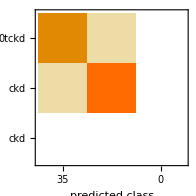
Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 80
Accuracy | (95.02.5) %
Accuracy baseline | (56.6.) %
Geometric mean of probabilities | 0.81 ± 0.044
Mean cross entropy | 0.211 ± 0.054
Single evaluation time | 5.19 ms/example
Batch evaluation speed | 4.18 examples/ms
-Graphics- |

```mathematica
(*export the acccuracy*)
myAccuracyDiag=ClassifierMeasurements[myClassify,myDataTest];
myAccuracyDiag["Report"]
```

Using the model

Saving the trained Predictor for future use

Batch Prediction

Batch Output